```mathematica
Grid[Partition[Tooltip[Show[ColorConvert[ColorData[#,"Image"],"RGB"],ImageSize->200],#]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
ic[x_]:={1/2 1/(2Zeta[3])(x/2)^2/(Exp[x/2]-1),1/8 Boole[1<x<9],1/2 x^2/Exp[x]}[[1]]
```

```mathematica
color="CMYKColors";
```

```mathematica
ColorConvert[ColorData[color,"Image"],"Grayscale"]
```

-Graphics-

```mathematica
tryCD[s_]:=If[DirectoryQ[s],SetDirectory[s],];tryCD["/home/kasper/Documents/KULeuven/PhD/Photon diffusion"];tryCD["/localhome/u0131889/Dropbox/Documents/KULeuven/PhD/Photon diffusion"]
```

/localhome/u0131889/Dropbox/Documents/KULeuven/PhD/Photon diffusion

```mathematica
dir="data-lineair";
```

```mathematica
Monitor[dataraw={};Do[
AppendTo[dataraw, Import[i]]
,{i,FileNames[dir<>"/hist*dat"]}],i];
Monitor[nraw={};Do[
AppendTo[nraw, Import[i]]
,{i,FileNames[dir<>"/occu*dat"]}],i];Length[dataraw]
```

21

```mathematica
xsraw=Import[dir<>"/xs.dat","List"]
```

{0.603197,1.87157,1.53781,1.56729,0.847643,1.40026,4.12043,1.44325,3.59009,7.7692,1.41605,1.18776,4.08303,2.47645,2.05633,999970,4.15763,3.31927,2.0703,2.31193,0.475703,3.16902,1.53433,4.33132,1.08469,1.96683,5.897,1.3055,1.98746,1.08468,4.19332}
 |  |  |  |

```mathematica
{bins2,counts}=HistogramList[xsraw,{Range[0,0.1,0.005]~Join~Rest@Range[0.1,20,0.05]},"PDF"];bins=MovingAverage[bins2,2];data=Transpose[{bins,counts}];
```

```mathematica
filename=Import[dir<>"/params.txt"]
```

N-1e6.00_t-20_ic-boltzmann_reset_rate-0.0013_divisor-160.00

```mathematica
data2=dataraw[[-1]];
```

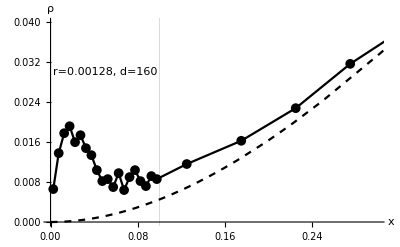

```mathematica
μ=0.081129;μ=0;histplot=Show[
ListPlot[{data},PlotRange->{{0,0.3},{0,0.04}},Joined->{True,True},Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotStyle->Black,GridLines->{{0.1},{}},PlotMarkers->{{Automatic, Medium}},Epilog->{ Text["r="<>ToString[0.00128]<>", d="<>ToString[160],{0.05,0.03}]}
],
Plot[{If[True,1/2 x^2/Exp[x],1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)],1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["spd_"<>filename<>".pdf",histplot];
```

```mathematica
Clear[plot];plot[r_,d_]:=plot[r,d]=Module[{dir,xsraw,bins,bins2,counts,filename,μ,histplot},
dir="data-r-"<>ToString[r]<>"-d-"<>ToString[d];
xsraw=Import[dir<>"/xs.dat","List"];
{bins2,counts}=HistogramList[xsraw,{Range[0,0.1,0.005]~Join~Rest@Range[0.1,10,0.05]},"PDF"];bins=MovingAverage[bins2,2];data=Transpose[{bins,counts}];
filename=Import[dir<>"/params.txt"];
μ=0.081129;μ=0;histplot=Show[
ListPlot[{data},PlotRange->{{0,0.2},{0,0.10}},Joined->{True,True},Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotStyle->Black,GridLines->{{0.1},{}},PlotMarkers->None,Epilog->{ Text["r="<>ToString[(1.0*^-5 2^r)]<>", d="<>ToString[10 2^d],{0.05,0.08}]}
],
Plot[{If[False,1/2 x^2/Exp[x],1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)]},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
];
histplot]
```

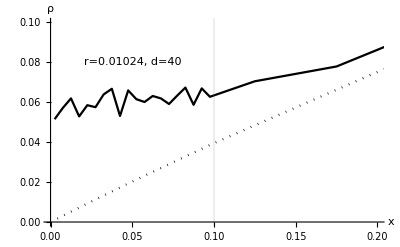

```mathematica
p=plot[10,2]
```

```mathematica
Table[a,{a,1,10,2}]
```

{1,3,5,7,9}

```mathematica
Monitor[c=Grid[Table[plot[a,b], {a,1,9},{b,1,10}]],{a,b}]
```

-Graphics-

```mathematica
Export["c.pdf",c]
```

c.pdf

```mathematica
Select
```

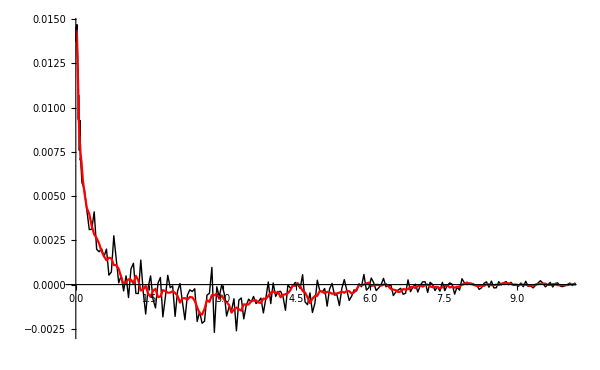

```mathematica
excess={#[[1]],#[[2]]-1/(2PolyLog[3,Exp[-μ]])(#[[1]])^2/(Exp[#[[1]]+μ]-1)}&/@data[[;;]];excessplot=ListPlot[{excess,MovingAverage[excess,5]},Joined->True,PlotStyle->{{Thin,Black},Red},PlotRange->{{0,10},All}]
```

```mathematica
Export["excess_"<>filename<>".pdf", excessplot];
```

```mathematica
ndata=nraw[[-1;;]];
```

```mathematica
n2=Table[{ndata[[1,i,1]],Mean[ndata[[;;,i,2]]]},{i,20*20}];
```

```mathematica
tplot=Show[
ListPlot[Last@TakeList[{#[[1]],(#[[1]]+μ)/Log[1+1/(#[[2]])]}&/@(n2[[1;;10*20]]),{0,All}],PlotRange->{{0,0.5},All},Joined->{True,False},PlotTheme->"Monochrome",AxesLabel->{"x","T_eff"},PlotMarkers->None]]
```

```mathematica
nearzeros=Table[{1*^-5*2^i,(1*^-5*2^i)^-0.6 ToExpression@Import["data-r-"<>ToString[i]<>"-d-"<>ToString[j]<>"/nearzero.txt"]},{j,10},{i,4,10}];
```

General::stop: Further output of Import::nffil will be suppressed during this calculation.

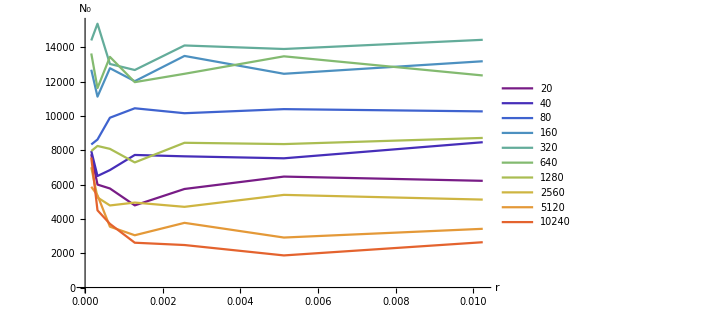

```mathematica
nearplot=ListPlot[nearzeros,Joined->True,PlotLegends->Table[10*2^j,{j,10}],PlotStyle->ColorData["Rainbow"]/@Range[0,1,1/10],AxesLabel->{"r","N_0"}]
```

```mathematica
Export["near.pdf",nearplot]
```

near.pdf

```mathematica
nearzeros2=Table[{10*2^j,(1*^-5*2^i)^-0.6 ToExpression@Import["data-r-"<>ToString[i]<>"-d-"<>ToString[j]<>"/nearzero.txt"]},{i,10},{j,10}];
```

```mathematica
nearzeros3=Table[{10*2^j,(1*^-5*2^10)^-0.6 900Exp[-(0.4(Log[10 2^j]-Log[300])/1)^2]},{j,8}];
```

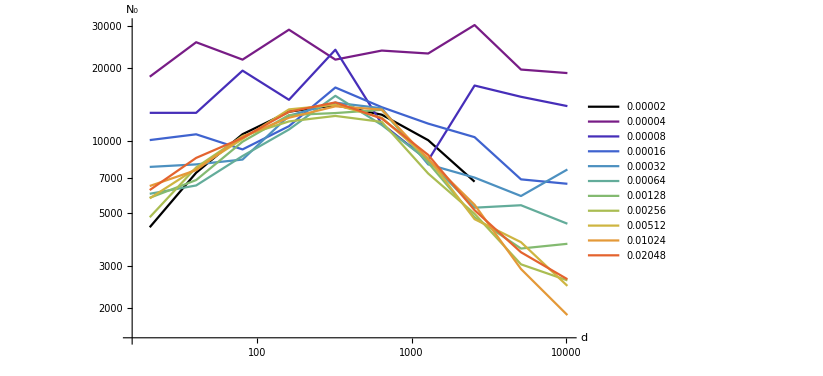

```mathematica
nearplot2=ListLogLogPlot[{nearzeros3}~Join~nearzeros2,Joined->True,PlotLegends->Table[1.0*^-5*2^i,{i,19}],PlotStyle->{Black}~Join~(ColorData["Rainbow"]/@Range[0,1,1/10]),AxesLabel->{"d","N_0"}]
```

```mathematica
Export["near2.pdf",nearplot2]
```

near2.pdf

```mathematica
NIntegrate[1/(2Zeta[3])x^2/(Exp[x]-1),{x,0,0.01}]*1*^6
```

20.7284

```mathematica
Export["temp_" <> filename <> ".pdf", tplot]
```

temp_N-1e5.95_t-10_Z-0.9000_reset_rate-0.0001_interval-0.10.pdf

```mathematica
ns=Import["data/n.dat"];
```

```mathematica
nplot=Show[
ListPlot[ns[[;;;;100]],PlotLegends->Automatic,Joined->True,PlotRange->All],
Plot[{Z[b,k,c]},{x,0,1000},PlotTheme->"Monochrome"]
]
```

```mathematica
Export["n "<>filename<>".pdf",nplot];
```

```mathematica
c=1/100;b=00/100;k=4/10;
```

```mathematica
x0=1/10;
```

```mathematica
h[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}]
```

```mathematica
Clear[Z];Z[b_,k_,c_]:=Z[b,k,c]=Module[{h2},
h2[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}];
NIntegrate[1/(2Zeta[3])xx^2/(Exp[h2[xx]]-1),{xx,0,∞}]]
```

```mathematica
pplot=histplot=Show[
ListPlot[data2,PlotRange->{{0,10},All},Joined->True,PlotStyle->Table[ColorData[color,i/(Length[data]-1)],{i,0,Length[data]-1}],(*PlotLegends->BarLegend[{"CMYKColors",{0,2}}],*)Ticks->{Automatic,None},AxesLabel->{"x","ρ"}
],
Plot[{1/(2Zeta[3])x^2/(Exp[x]-1)(*,1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)*)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["compare " <>filename<>".pdf",pplot]
```

compare N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems.pdf

```mathematica
NDSolve[{
D[u[t,x],t]==D[u[t,x],x,x]-u[t,x]+10u[t,10x],
u[0,x]==Exp[-x^2/2],u[t,-20]==u[t,+20]==0},u,{x,-20,+20},{t,0,10}]
```

NDSolve::conarg: The arguments should be ordered consistently.

NDSolve::delpde: Delay partial differential equations are not currently supported by NDSolve.

NDSolve[{u^(1,0)[t,x]==-u[t,x]+10 u[t,10 x]+u^(0,2)[t,x],u[0,x]==ⅇ^(-x^2/2),u[t,-20]==u[t,20]==0},u,{x,-20,20},{t,0,10}]

```mathematica
Plot[{1/QPochhammer[-k^2,1/100],1/QPochhammer[-(k/10)^2,1/100](1+k^2)^-1},{k,-10,+10},PlotRange->All]
```

```mathematica
Product[1/(1+(k/10^m)^2)1/10^m,{m,0,∞}]
```

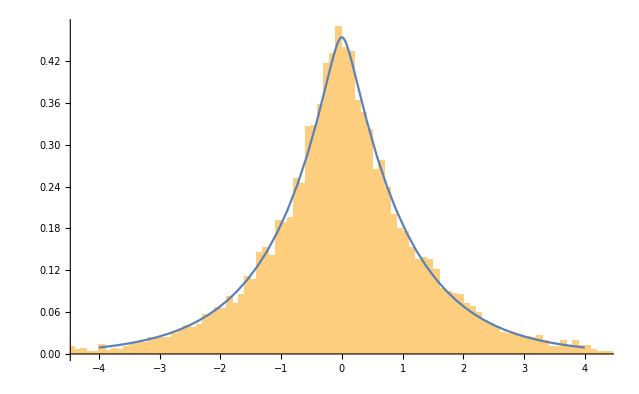

```mathematica
Show[
Histogram[a,{0.1},"PDF"],
Plot[f[x],{x,-4,+4}]]
```

```mathematica
μ=0.0811294
```

0.0811294

```mathematica
Clear[μ]
```

```mathematica
f[x_]:=1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)(-p)+p 1/δ Exp[-x/δ];FullSimplify[2x f[x]-x^2 f'[x]-x^2 f[x]-f[x]^2,0<x&&δ>0&&0<p<1]
```

p (((-0.392947-0.181609 p) x^4)/((0.922074-1. ⅇ^x)^2)-(ⅇ^(-(2 x)/δ) p)/δ^2+(2 ⅇ^(-x/δ) x)/δ+(ⅇ^(-x/δ) x^2 (-0.922074+ⅇ^x (1.-1. δ)+0.922074 δ+0.852312 p δ))/((-0.922074+1. ⅇ^x) δ^2))

```mathematica
FullSimplify[(ⅇ^(-(2 x)/δ) p (-p-ⅇ^(x/δ) x (x (-1+δ)-2 δ)))/δ^2+((-1+p) x^2 (x^2-p x^2+(-2 x^2+(4 ⅇ^(-x/δ) (-1+ⅇ^(x+μ)) p)/δ) PolyLog[3,ⅇ^-μ]))/(4 (-1+ⅇ^(x+μ))^2 PolyLog[3,ⅇ^-μ]^2)/.x->2δ]
```

-(p (p+4 ⅇ^2 (-2+δ) δ^2))/(ⅇ^4 δ^2)-(4 (-1+p) δ (ⅇ^2 (-1+p) δ^3+(p-ⅇ^(2 δ+μ) p+2 ⅇ^2 δ^3) PolyLog[3,ⅇ^-μ]))/(ⅇ^2 (-1+ⅇ^(2 δ+μ))^2 PolyLog[3,ⅇ^-μ]^2)

```mathematica
NSolve[-p (-2+2^(1/3) (p/(1-p))^(1/3))==0.01,p]
```

{{p→0.796962},{p→0.00563251}}

```mathematica
0.0004431247075131062
```

```mathematica
Solve[(1-δ h)δ^2/2==h δ h,
```

```mathematica
Series[((ⅇ^(-(2 x)/δ) p (-p-ⅇ^(x/δ) x (x (-1+δ)-2 δ)))/δ^2+((-1+p) x^2 (x^2-p x^2+(-2 x^2+(4 ⅇ^(-x/δ) (-1+ⅇ^(x+μ)) p)/δ) PolyLog[3,ⅇ^-μ]))/(4 (-1+ⅇ^(x+μ))^2 PolyLog[3,ⅇ^-μ]^2)),{p,0,1}]
```

(0.248569 x^4)/((-1+ⅇ^(0.0811294+x))^2)+((0.213602 x^2 (-0.163702 x^2-(4.3274 ⅇ^(-x/δ) (-1+ⅇ^(0.0811294+x)))/δ))/((-1+ⅇ^(0.0811294+x))^2)-(ⅇ^(-x/δ) x (x (-1+δ)-2 δ))/δ^2) p+O[p]^2

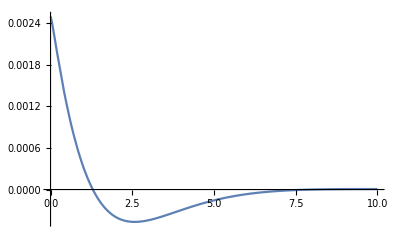

```mathematica
Plot[1/(2PolyLog[3,Exp[-μ]])x^2/(Exp[x+μ]-1)(-p)+p 1/δ Exp[-x/δ]/.{p->0.005,δ->2},{x,0,10},PlotRange->All]
```

```mathematica
Solve[-p(-2+0.1)==0.0005,p]
```

{{p→0.000263158}}

```mathematica
(-((-1+p) δ^4 (-1+p+2 Z Zeta[3]))/(4 (-1+ⅇ^(δ+μ))^2 Z^2 Zeta[3]^2)/.{μ->0,Z->1})//FullSimplify
```

-((-1+p) δ^4 (-1+p+2 Zeta[3]))/(4 (-1+ⅇ^δ)^2 Zeta[3]^2)

```mathematica
Series[-((-1+p) δ^4 (-1+p+2 Zeta[3]))/(4 (-1+ⅇ^δ)^2 Zeta[3]^2),{p,0,2},{δ,0,4}]//Normal
```

p^2 (-δ^2/(4 Zeta[3]^2)+δ^3/(4 Zeta[3]^2)-(5 δ^4)/(48 Zeta[3]^2))+p ((δ^2 (1-Zeta[3]))/(2 Zeta[3]^2)+(δ^3 (-1+Zeta[3]))/(2 Zeta[3]^2)-(5 δ^4 (-1+Zeta[3]))/(24 Zeta[3]^2))+(δ^2 (-1+2 Zeta[3]))/(4 Zeta[3]^2)-(δ^3 (-1+2 Zeta[3]))/(4 Zeta[3]^2)+(5 δ^4 (-1+2 Zeta[3]))/(48 Zeta[3]^2)

```mathematica
p^2 (-δ^2/(4 Zeta[3]^2)+δ^3/(4 Zeta[3]^2)-(5 δ^4)/(48 Zeta[3]^2))+p ((δ^2 (1-Zeta[3]))/(2 Zeta[3]^2)+(δ^3 (-1+Zeta[3]))/(2 Zeta[3]^2)-(5 δ^4 (-1+Zeta[3]))/(24 Zeta[3]^2))+(δ^2 (-1+2 Zeta[3]))/(4 Zeta[3]^2)-(δ^3 (-1+2 Zeta[3]))/(4 Zeta[3]^2)+(5 δ^4 (-1+2 Zeta[3]))/(48 Zeta[3]^2)/.δ->0.1
```

0.00219655-0.000632182 p-0.00156437 p^2

```mathematica
PolyLog[3,Exp[-0.0811]]/Zeta[3]
```

0.900033

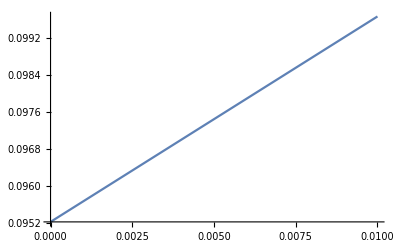

```mathematica
With[{δ=1,μ=0.0,Z=PolyLog[3,Exp[-μ]]/Zeta[3]},Plot[{-(p (p+4 ⅇ^2 (-2+δ) δ^2))/(ⅇ^4 δ^2)-(4 (-1+p) δ (ⅇ^2 (-1+p) δ^3+(p-ⅇ^(2 δ+μ) p+2 ⅇ^2 δ^3) PolyLog[3,ⅇ^-μ]))/(ⅇ^2 (-1+ⅇ^(2 δ+μ))^2 PolyLog[3,ⅇ^-μ]^2)},{p,0 ,0.01},PlotRange->All]]
```